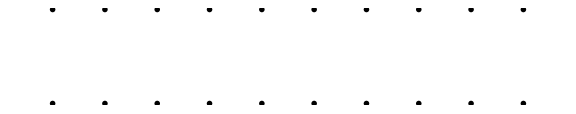

```mathematica
GraphicsGrid[Partition[Table[With[{hist=TakeWhile[{#1,#2[[;;7]]}&@@@TuringMachine[445,{{1,7},{IntegerDigits[n,2,7],0}},10],#[[1,3]]<=0&]},Show[{RulePlot[TuringMachine[445],Append[hist,MapAt[#+{0,1,1}&,hist[[-1]],1]],],Graphics[{GrayLevel[.85],EdgeForm[{Thin,GrayLevel[.15]}],Table[Rectangle[{Length[hist[[1,2]]],y}],{y,0,Length[hist]}]}]}]],{n,1,20}],10],]
```